# q q̄→μ μ in EW theory (SMQCD ): GENERIC CHARGES

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SMQCD",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
```

## SMQCD: Feynman rules and Diagrams

## Rules

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3}
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3}
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QLl→-1,QUl→2/3,QDl→-1/3}

{QLr→-1,QUr→2/3,QDr→-1/3}

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SMQCD",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

## Feynman Diagrams

Function tracecolour selects diagrams where colour conservation in present (if output=0 diagram is not considered)

```mathematica
tracecolour[diag_]:=Module[{sunt,trsunt,sumover,g,tab},
diagram=Table[Part[diag,{i}][[1,3]],{i,1,Length[diag]}];
(*trace closed fermion loop*)
tr=Table[Cases[diagram[[i]],_MatrixTrace,Infinity],{i,1,Length[diagram]}];
(*fermionchain without tr*)
input2=Table[DeleteCases[diagram[[i]],_MatrixTrace,Infinity]//.MASSES,{i,1,Length[diagram]}];
sumover=Table[Cases[input2,_SumOver,Infinity],{i,1,Length[input2]}];


Table[If[MemberQ[tr[[i]],SUNT[g_,col_,col_],Infinity]&&MemberQ[sumover[[i]],SumOver[col_,_]], g[i]=0,g[i]=1],{i,1,Length[tr]}];
tab=Table[g[i],{i,1,Length[diagram]}];
tab
];
```

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[2, 2 -> 2, SelfEnergiesOnly];
ins2 = DiagramSelect[InsertFields[tops2, process],Count[LoopFields[##],V[5,_]]===1&];
ins22=DiagramSelect[ins2,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

```mathematica
selfff=CreateFeynAmp[ins22];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 24 Particles amplitudes

> Top. 2: 48 Particles amplitudes

in total: 72 Particles amplitudes

Sequence[]

> Top. 1 aebe/cfdf/egfh1g1h212g2h.m, 0 diagrams

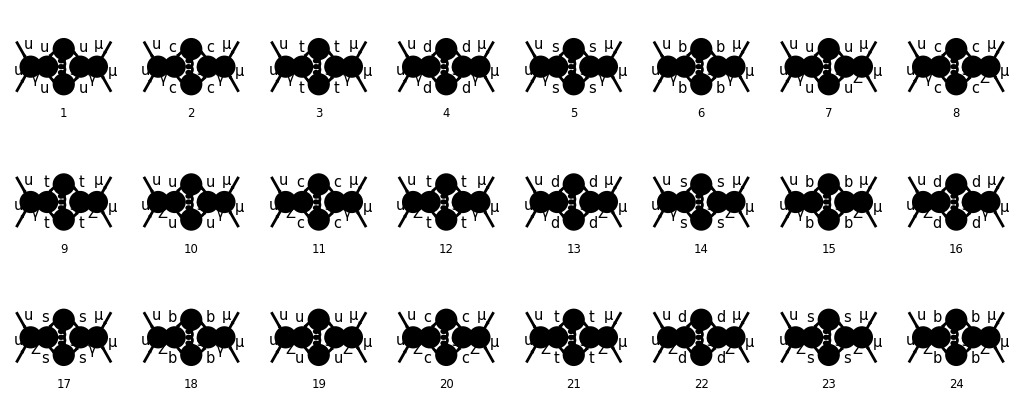

> Top. 1 aebe/cfdf/egfhgh1g21212h.m, 0 diagrams

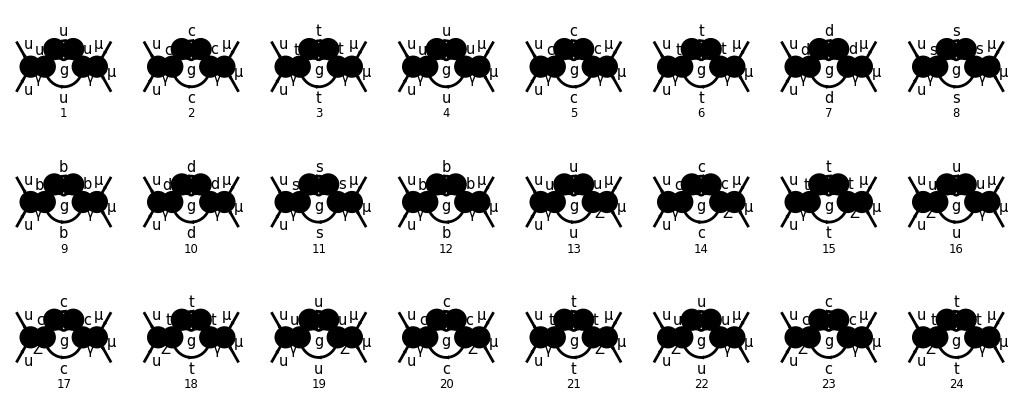

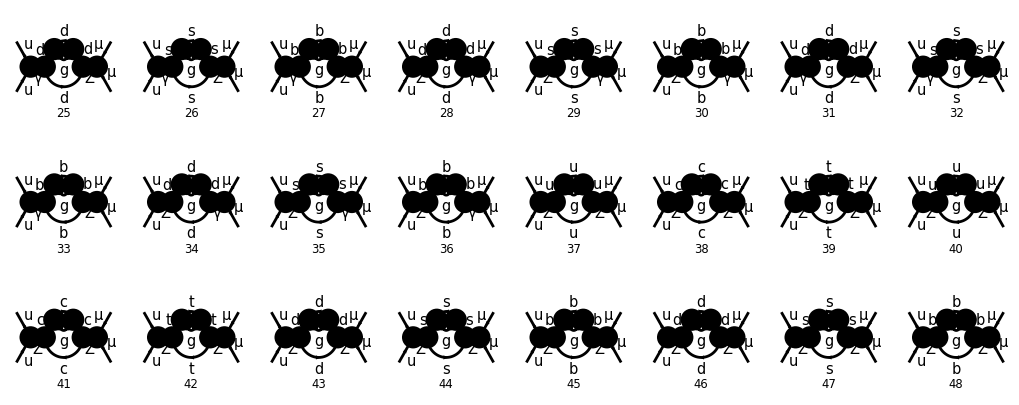

```mathematica
Position[tracecolour[selfff],0]//.List->Sequence(*0 diagrams deleted*)
Table[Paint[ins22[[i]],ColumnsXRows->{8,3},Numbering->Simple,
SheetHeader->None,ImageSize->{1020,406}],{i,1,Length[ins22]}];
```

## Vertices

```mathematica
tops4 = CreateTopologies[2, 2 -> 2, TrianglesOnly];
ins4 =DiagramSelect[InsertFields[tops4, process],Count[LoopFields[##],V[5,_]]===1&];
ins44=DiagramSelect[ins4,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

```mathematica
(*Table[Paint[ins44[[i]],ColumnsXRows->{8,1},Numbering->Simple,FieldNumbers->True,
SheetHeader->None,ImageSize->{1012,156}],{i,1,Length[ins4]}];*)
verttt=CreateFeynAmp[ins4];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

> Top. 2: 110 Particles amplitudes

> Top. 3: 14 Particles amplitudes

> Top. 4: 7 Particles amplitudes

> Top. 5: 12 Particles amplitudes

> Top. 6: 13 Particles amplitudes

> Top. 7: 13 Particles amplitudes

> Top. 8: 50 Particles amplitudes

in total: 233 Particles amplitudes

> Top. 1 HFlip[aebe/cfdg/eh1f1g212f2hgh.m], 0 diagrams

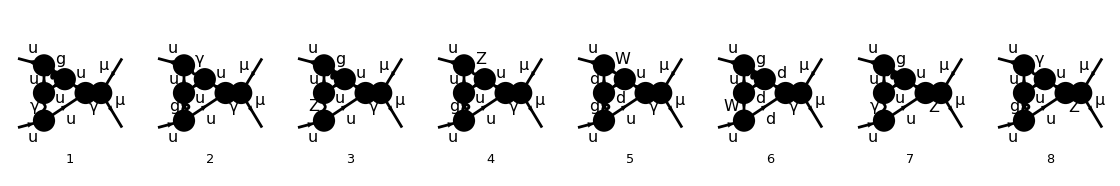

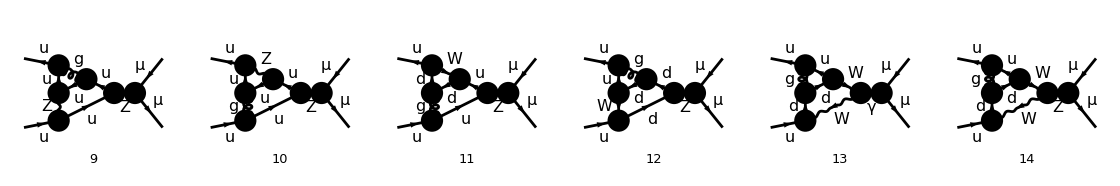

> Top. 1 HFlip[aebe/cfdg/ehfg1f1h212g2h.m], 0 diagrams

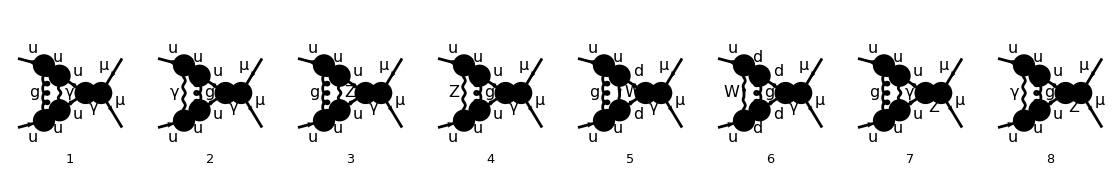

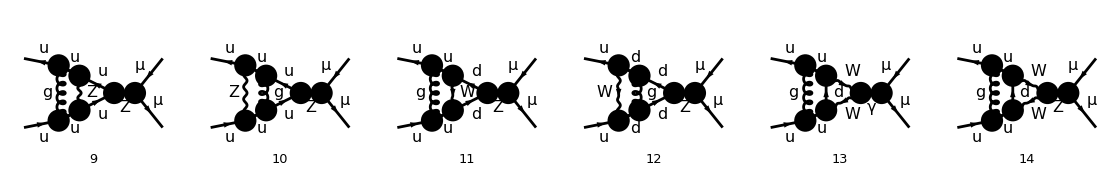

> Top. 1 VFlip[HFlip[aebe/cfdg/eh1f1g212f2hgh.m]], 0 diagrams

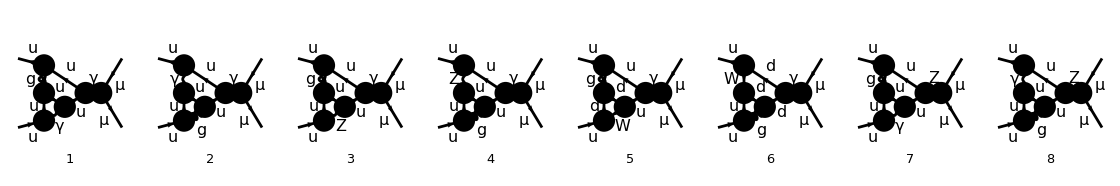

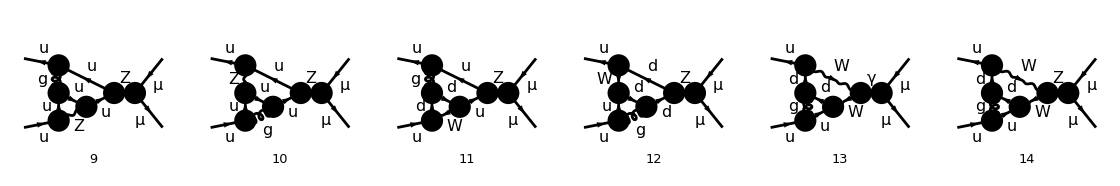

> Top. 1 aebf/cgdh/212g2h1e1fefgh.m, 0 diagrams

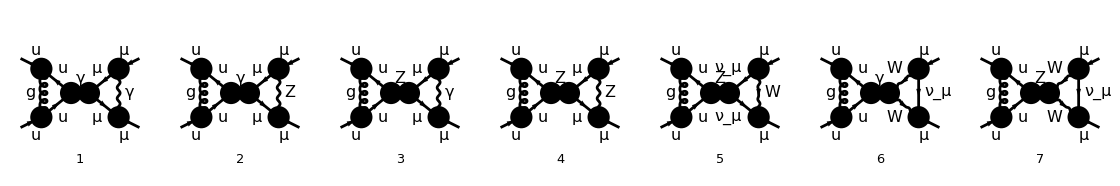

> Top. 1 aebf/cgdg/gh1e1f1h2e2f2h.m, 0 diagrams

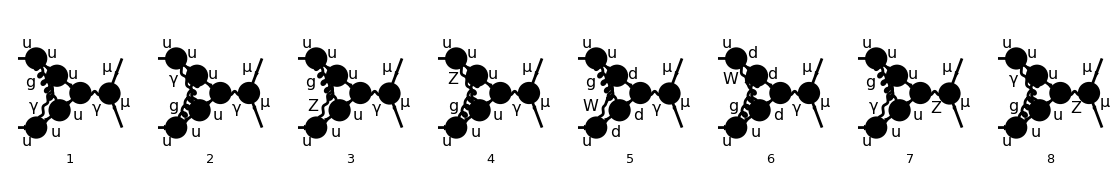

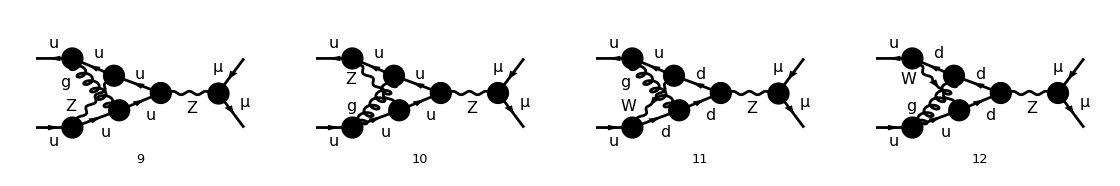

> Top. 1 aebf/cgdg/ghef1e21212hfh.m, 0 diagrams

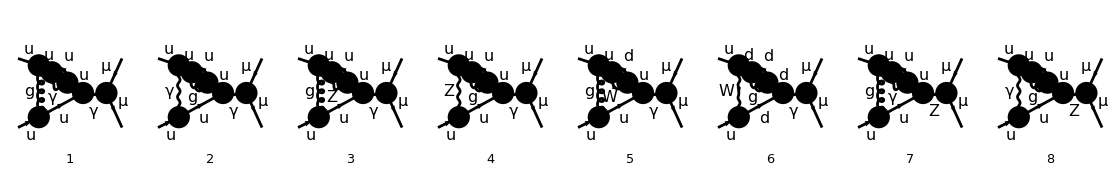

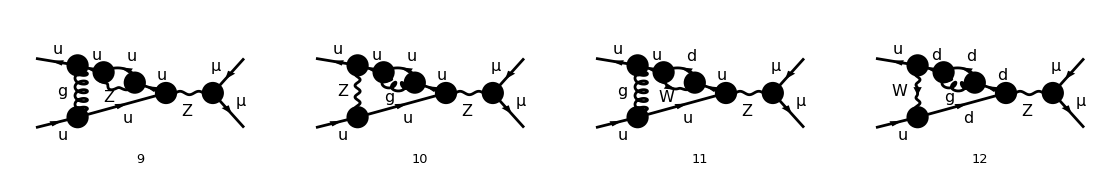

> Top. 1 VFlip[aebf/cgdg/ghef1e21212hfh.m], 0 diagrams

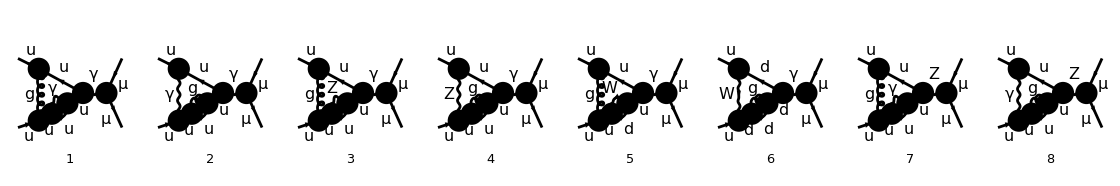

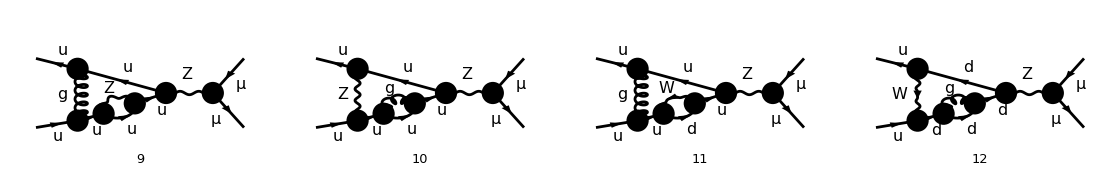

> Top. 1 aebf/cgdg/gheh1e21212ffh.m, 0 diagrams

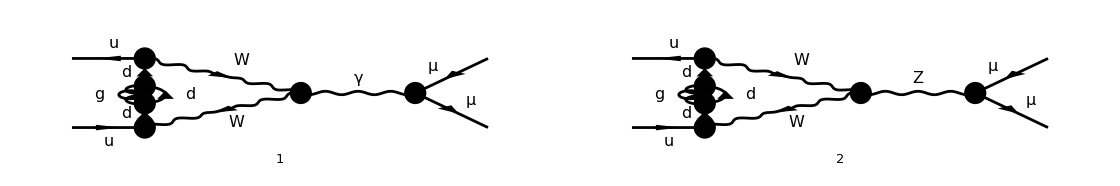

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

> Top. 2: 14 Particles amplitudes

> Top. 3: 14 Particles amplitudes

> Top. 4: 7 Particles amplitudes

> Top. 5: 12 Particles amplitudes

> Top. 6: 12 Particles amplitudes

> Top. 7: 12 Particles amplitudes

> Top. 8: 2 Particles amplitudes

in total: 87 Particles amplitudes

```mathematica
pvt=Position[tracecolour[verttt],0]//.List->Sequence;
vert2=DiagramDelete[ins44,pvt];(*diagrams without colour conservation are deleted*)
Table[Paint[vert2[[i]],ColumnsXRows->{8,1},Numbering->Simple,
SheetHeader->None,ImageSize->{1120,186}],{i,1,Length[vert2]}];
verttt=CreateFeynAmp[vert2];
```

## Boxes

```mathematica
tops5 = CreateTopologies[2, 2 -> 2, BoxesOnly]; 
ins5 =DiagramSelect[InsertFields[tops5, process],Count[LoopFields[##],V[5,_]]===1&];
ins55=DiagramSelect[ins5,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

```mathematica
(*Table[Paint[ins55[[i]],Numbering->Simple,
SheetHeader ->None,ColumnsXRows->{5,1},ImageSize->{812,256}],{i,1,Length[ins5]}];*)
box1=CreateFeynAmp[ins5];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 4 Particles amplitudes

> Top. 4: 5 Particles amplitudes

> Top. 5: 4 Particles amplitudes

> Top. 6: 5 Particles amplitudes

> Top. 7: 24 Particles amplitudes

> Top. 8: 24 Particles amplitudes

> Top. 9: 24 Particles amplitudes

> Top. 10: 24 Particles amplitudes

> Top. 11: 4 Particles amplitudes

> Top. 12: 5 Particles amplitudes

in total: 132 Particles amplitudes

> Top. 1 aebf/cgdh/1e1g212e2ffhgh.m, 0 diagrams

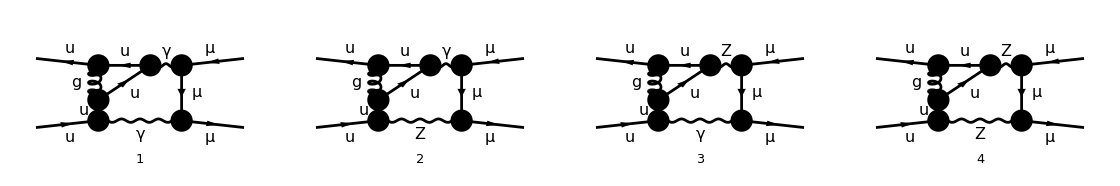

> Top. 1 aebf/cgdh/1e1h212e2ffggh.m, 0 diagrams

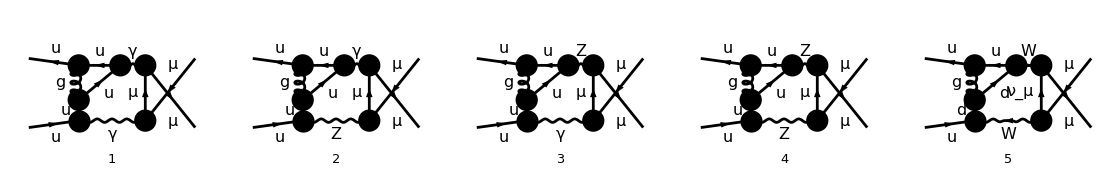

> Top. 1 aebf/cgdh/ef1e1g212f2hgh.m, 0 diagrams

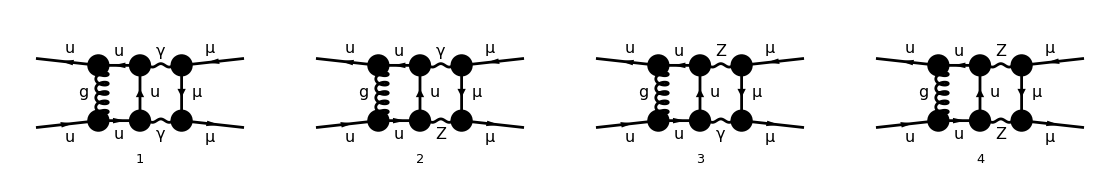

> Top. 1 aebf/cgdh/ef1e1h212f2ggh.m, 0 diagrams

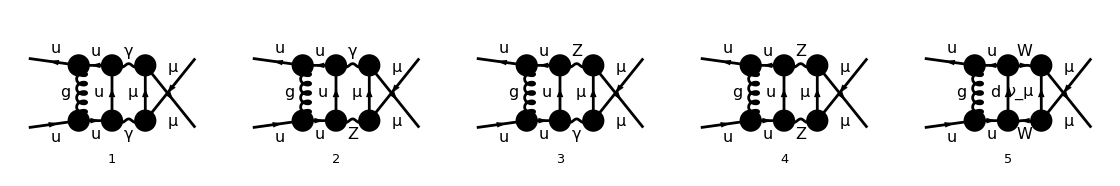

> Top. 1 VFlip[aebf/cgdh/1e1g212e2ffhgh.m], 0 diagrams

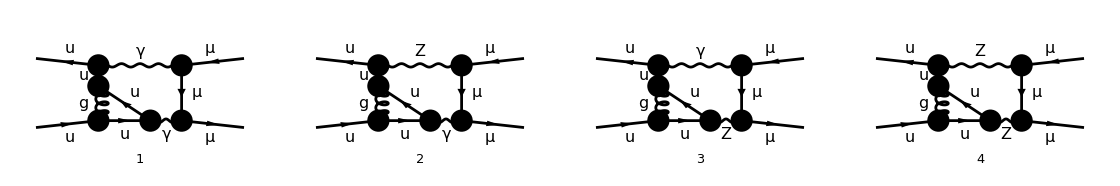

> Top. 1 VFlip[aebf/cgdh/1e1h212e2ffggh.m], 0 diagrams

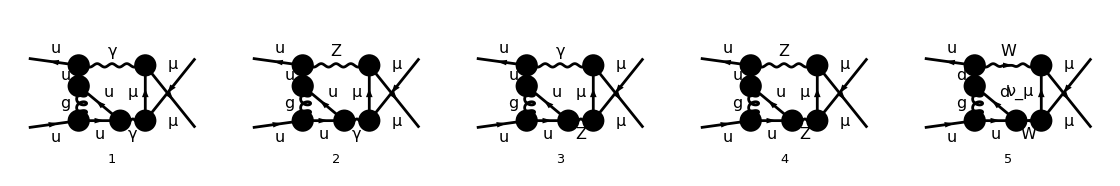

> Top. 1 aebf/cgdh/eg1e21212ffhgh.m, 0 diagrams

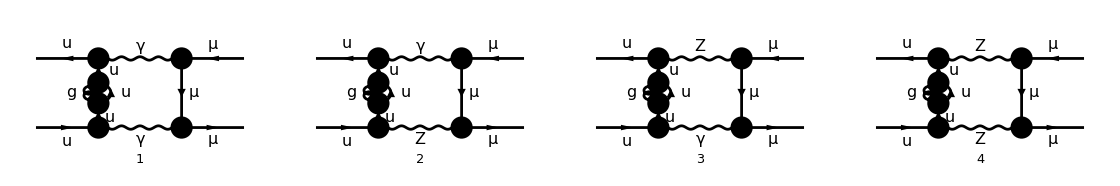

> Top. 1 aebf/cgdh/eh1e21212ffggh.m, 0 diagrams

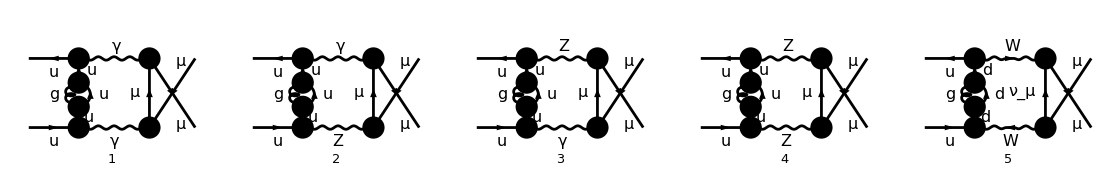

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 4 Particles amplitudes

> Top. 4: 5 Particles amplitudes

> Top. 5: 4 Particles amplitudes

> Top. 6: 5 Particles amplitudes

> Top. 7: 4 Particles amplitudes

> Top. 8: 5 Particles amplitudes

in total: 36 Particles amplitudes

```mathematica
pbx=Position[tracecolour[box1],0]//.List->Sequence;
box2=DiagramDelete[ins55,pbx];(*diagrams without colour conserv. are deleted*)
Table[Paint[box2[[i]],ColumnsXRows->{8,1},Numbering->Simple,
SheetHeader->None,ImageSize->{1120,186}],{i,1,Length[box2]}];
box1=CreateFeynAmp[box2];
```

## Diagrams simplification (box couples)

### classification

```mathematica
(*set variabili semplificate*)
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
Q2=FourMomentum[Internal,2];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

```mathematica
boxx1=Table[{Union[Cases[Part[box1,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],i},
{i,1,Length[box1]}];
boxx2=Sort[boxx1//.{PropagatorDenominator[Plus[Q1,Times[-1,K1]],0]->tdenQ1,PropagatorDenominator[Plus[Q1,Times[-1,K2]],0]->udenQ1,
PropagatorDenominator[Plus[Q2,Times[-1,K1]],0]->tdenQ2,PropagatorDenominator[Plus[Q2,Times[-1,K2]],0]->udenQ2}];
boxx3=Gather[DeleteCases[boxx2,tdenQ1|udenQ1|tdenQ2|udenQ2,Infinity],First[#1]==First[#2]&];
bbox=Sort[Table[Cases[boxx3[[i]],_Integer,{2}],{i,1,Length[boxx3]}]]
```

{{9},{18},{27},{36},{1,5},{2,6},{3,7},{4,8},{10,14},{11,15},{12,16},{13,17},{19,23},{20,24},{21,25},{22,26},{28,32},{29,33},{30,34},{31,35}}

```mathematica
totbbox=Table[{Part[box1,{bbox[[i]][[1]]}][[1,3]],Part[box1,{bbox[[i]][[2]]}][[1,3]]},{i,5,Length[bbox]}];
totbboxw=Table[Part[box1,{bbox[[i]][[1]]}][[1,3]],{i,1,4}];
```

```mathematica
(*esempio*)
tboxzz=totbbox[[1,1]];(*from 1 to 16*)
denomt=Union[Cases[tboxzz//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K1]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K1]],0],Infinity]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)/.List->Sequence
uboxzz=totbbox[[1,2]];
denomu=Union[Cases[uboxzz//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K2]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K2]],0],Infinity]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)/.List->Sequence
wwbox=totbboxw[[4]];(*from1 to 4*)
denomw=Union[Cases[wwbox//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K2]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K2]],0],Infinity]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)/.List->Sequence
```

Sequence[1/(q2-k1)^2]

Sequence[1/(q2-k2)^2]

Sequence[1/(q1-k2)^2]

mettere 1 per fotone e 2 per z e tboxzz loop diagram

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES;
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}] 
colourborn=Union[Cases[born,(*_SumOver|*)_IndexDelta,Infinity]]
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times/.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
(*bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)*)
```

{CONJ[v̄[p2,0].(-ⅈ EL QUl ga[Lorbn1].om_--ⅈ EL QUr ga[Lorbn1].om_+).u[p1,0]],CONJ[ū[k1,0].(-ⅈ EL QLl ga[Lorbn2].om_--ⅈ EL QLr ga[Lorbn2].om_+).v[k2,0]]}

{IndexDelta[Col1,Col2]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

#### Colour trace

```mathematica
(*LOOP DIAGRAM COLOUR*)(*self energies sunt in tr loop fermion*)
tabcolor[diag_]:=Module[{t},
diagram=diag;
tbcolour=Table[tb=Part[diagram,{i}][[1,3]];
(*trace closed fermion loop*)
tr=Cases[tb,_MatrixTrace,Infinity];
(*fermionchain without tr*)
input2=DeleteCases[tb,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[trsunt,sunt,colourborn],{i,1,Length[diagram]}];

tbcolour=Union[tbcolour//.{SUNT[g1_,c2_,c5_],SUNT[g2_,c5_,c2_],x__}->{TR[SUNT[g1],SUNT[g2]],x}//.{SUNT[g1_,c1_,c5_],SUNT[g2_,c5_,c2_],IndexDelta[c1_,c2_]}->TR[SUNT[g1],SUNT[g2]]];

tbcolour
];
```

```mathematica
tabcolor[box1]
```

{TR[SUNT[Glu5],SUNT[Glu5]]}

```mathematica
tabcolor[selfff]
```

{{TR[SUNT[Glu5],SUNT[Glu5]],IndexDelta[Col1,Col2],IndexDelta[Col1,Col2]}}

SUNT[a,k,l] SUNT[b,i,j] IndexDelta[j,k] IndexDelta[a,b]=CF IndexDelta[i,l]
Tr(T a T a ) = C(r)dim(G).

#### Loop diagrams propagators

Divisione in termini dipendenti da gauge e indipendenti

```mathematica
tpropag=DeleteCases[tboxzz//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
upropag=DeleteCases[uboxzz//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
wpropag=DeleteCases[wwbox//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
```

-(g[Lor1,Lor2] g[Lor3,Lor4] g[Lor5,Lor6] 1/(q1)^2 1/(q2)^2 1/(q1+q2)^2 1/(q2-k1)^2 1/(q2-k1-k2)^2 1/(p2+q2-k1-k2)^2 1/(-(p2)+q1+k1+k2)^2)/(256 π^8)

-(g[Lor1,Lor2] g[Lor3,Lor4] g[Lor5,Lor6] 1/(q1)^2 1/(q2)^2 1/(q1+q2)^2 1/(q2-k2)^2 1/(q2-k1-k2)^2 1/(p2+q2-k1-k2)^2 1/(-(p2)+q1+k1+k2)^2)/(256 π^8)

-(g[Lor1,Lor2] g[Lor3,Lor4] g[Lor5,Lor6] 1/(-MW2+(q1)^2) 1/(q2)^2 1/(q1-k2)^2 1/(-MW2+(q1-k1-k2)^2) 1/(-(p2)-q1+q2+k1+k2)^2 1/(p2+q1-k1-k2)^4)/(256 π^8)

```mathematica
(*propagatore box, parte in comune fra t e u. propagatore box W*)
denomt1=Union[Cases[tboxzz//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K1]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K1]],0],Infinity]]/.List->Sequence;
denomu1=Union[Cases[uboxzz//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K2]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K2]],0],Infinity]]/.List->Sequence;
denomw1=Union[Cases[wwbox//.MASSES,PropagatorDenominator[Plus[Q1,Times[-1,K2]],0]|PropagatorDenominator[Plus[Q2,Times[-1,K2]],0],Infinity]]/.List->Sequence;

ptot=DeleteCases[tpropag,denomt1,Infinity]+DeleteCases[upropag,denomu1,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
ptotw=DeleteCases[wpropag,denomw1,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(128 π^8 (q1)^2 (q2)^2 (q1+q2)^2 (q2-k1-k2)^2 (p2+q2-k1-k2)^2 (-(p2)+q1+k1+k2)^2)

-(1/(p2+q1-k1-k2)^4 SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-MW2+(q1)^2) (q2)^2 (-MW2+(q1-k1-k2)^2) (-(p2)-q1+q2+k1+k2)^2)

#### Trace

```mathematica
trg[z___,-G5]:=-trg[z,G5];
trg[a_,b_,G5]:=0;
trg[a_,b_,c_,d_,G5]:=-4 I LC myEps[a,b,c,d];
trg[x___,G5,G5,y___]:=trg[x,y];
trg[x__,G5]:=0/;OddQ[Length[{x}]];
trg[q___,G5,y__]:=trg[q,y,G5](-1)^(Length[{y}]);
trg[a_,b_]:=4 SP[a,b];
trg[w__]:=0/;OddQ[Length[{w}]] && FreeQ[{w},G5];

(*TRACE*)
trg[x__]:=Module[{temp,temp1,temp2,i,temp3},

temp={x};
temp1=Delete[temp,1];
temp2=Table[Delete[temp1,i],{i,1,Length[temp1]}];
temp3=Sum[SP[temp[[1]],temp1[[i]]](-1)^(i+1)*Apply[trg,temp2[[i]]],{i,1,Length[temp2]}];
temp3=Expand[temp3];

temp3
];
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;

(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
(*calcolo traccia*)
trace2[chargesi_,statoi_,chargesf_,statof_]:=Module[{tr1i,tr2i,tr3i,tr1f,tr2f,tr3f,tracciai,tracciaf,chii,chff,tracei,tracef},

(*trace:*)
traceff[x___,DiracSpinor[z_,w_],DiracSpinor[z_,w_],y___]:=traceff[x,DiracSlash[z],y];(* ...u(p)u_bar(p) ... -> ...p_slash... *)(*sost. stato intermedio*)
traceff[DiracSpinor[z_,w_],x__,DiracSpinor[z_,w_]]:=traceff[DiracSlash[z],x];(* v_bar(p)...v(p) ->p_slash... *)(*sost. stato esterno*)

(*stato i*)
tr1i=ParallelTable[traceff[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff->move2;(*sposto proiettori in fondo*)
chii=Delete[chargesi,Position[tr1i,0,{1}]];(*cariche*)
tr2i=ParallelMap[Distribute,1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=DeleteCases[tr2i,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)
tracciai=tr3i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//Expand;

(*stato f*)
tr1f=ParallelTable[traceff[statof[[i]]/.List->Sequence],{i,1,Length[statof]}]//.traceff->move2;
chff=Delete[chargesf,Position[tr1f,0,{1}]];(*cariche*)
tr2f=ParallelMap[Distribute,1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},{2}];
tr3f=DeleteCases[tr2f,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
tracciaf=tr3f/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//Expand;

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},"\n stato f ",
1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

tracei=Thread[List[chii,tracciai]];
tracef=Thread[List[chff,tracciaf]];

Return[{tracei,tracef}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=ParallelTable[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=ParallelTable[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=ParallelTable[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[-P1,0],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[-K1,0],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=ParallelTable[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[-P1,0],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=ParallelTable[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=ParallelTable[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=ParallelTable[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[ParallelTable[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[ParallelTable[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,0],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=ParallelTable[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=ParallelTable[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=ParallelTable[move2@@tbf[[i]],{i,1,Length[tbf]}]//.move2->List;
tbf3=DeleteCases[tbf2,0,1];
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[ParallelTable[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[ParallelTable[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

prova1=trace2[chi,stati,chf,statf];

Return[{tr,prova1}](*closed fermion loop, trace*)
];
```

```mathematica
boxt=fermiontrace[tboxzz];
```

stato i {1/2 move2[gs[-(p1)],ga[Lor4],gs[q1],ga[Lor1],gs[q1+q2],ga[Lor3],gs[p2+q2-k1-k2],ga[Lor5],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[-(p1)],ga[Lor4],gs[q1],ga[Lor1],gs[q1+q2],ga[Lor3],gs[p2+q2-k1-k2],ga[Lor5],gs[p2],ga[Lorbn1],1+G5]}
 stato f {1/2 move2[gs[k2],ga[Lor6],gs[q2-k1],ga[Lor2],gs[-(k1)],ga[Lorbn2],1-G5],1/2 move2[gs[k2],ga[Lor6],gs[q2-k1],ga[Lor2],gs[-(k1)],ga[Lorbn2],1+G5]}

```mathematica
boxu=fermiontrace[uboxzz];
```

stato i {1/2 move2[gs[-(p1)],ga[Lor4],gs[q1],ga[Lor1],gs[q1+q2],ga[Lor3],gs[p2+q2-k1-k2],ga[Lor5],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[-(p1)],ga[Lor4],gs[q1],ga[Lor1],gs[q1+q2],ga[Lor3],gs[p2+q2-k1-k2],ga[Lor5],gs[p2],ga[Lorbn1],1+G5]}
 stato f {1/2 move2[gs[k2],ga[Lor2],gs[-(q2)+k2],ga[Lor6],gs[-(k1)],ga[Lorbn2],1-G5],1/2 move2[gs[k2],ga[Lor2],gs[-(q2)+k2],ga[Lor6],gs[-(k1)],ga[Lorbn2],1+G5]}

### Semplificazioni/sostituzioni

```mathematica
Table[{chargeIt[i]=boxt[[2,1,i,1]],
iepst[i]=Select[List@@boxt[[2,1,i,2]],MemberQ[#,_myEps,Infinity]&],
inepst[i]=Select[List@@boxt[[2,1,i,2]],FreeQ[#,_myEps,Infinity]&]}
,{i,1,Length[boxt[[2,1]]]}];

Table[{chargeFt[i]=boxt[[2,2,i,1]],
fepst[i]=Select[List@@boxt[[2,2,i,2]],MemberQ[#,_myEps,Infinity]&],
fnepst[i]=Select[List@@boxt[[2,2,i,2]],FreeQ[#,_myEps,Infinity]&]}
,{i,1,Length[boxt[[2,2]]]}];
```

```mathematica
Table[{chargeIu[i]=boxu[[2,1,i,1]],
iepsu[i]=Select[List@@boxu[[2,1,i,2]],MemberQ[#,_myEps,Infinity]&],
inepsu[i]=Select[List@@boxu[[2,1,i,2]],FreeQ[#,_myEps,Infinity]&]}
,{i,1,Length[boxu[[2,1]]]}];
Table[{chargeFu[i]=boxu[[2,2,i,1]],
fepsu[i]=Select[List@@boxu[[2,2,i,2]],MemberQ[#,_myEps,Infinity]&],
fnepsu[i]=Select[List@@boxu[[2,2,i,2]],FreeQ[#,_myEps,Infinity]&]}
,{i,1,Length[boxu[[2,2]]]}];
```

```mathematica
CHARGEt[1,1]={chargeIt[1],chargeFt[1]};
CHARGEu[1,1]={chargeIu[1],chargeFu[1]};
```

```mathematica
STATt[1,1]={ParallelMap[iepst[1]*#&,fepst[1]]//Expand,ParallelMap[inepst[1]*#&,fnepst[1]]}//.List->Plus;
```

```mathematica
STATu[1,1]={ParallelMap[iepsu[1]*#&,fepsu[1]]//Expand,ParallelMap[inepsu[1]*#&,fnepsu[1]]}//.List->Plus;
```

```mathematica
(*Table[{CHARGEt[i,j]={chargeIt[i],chargeFt[j]},STATt[i,j]={ParallelMap[iepst[i]*#&,fepst[j]]//Expand,ParallelMap[inepst[i]*#&,fnepst[j]]}//.List->Plus},{i,1,2},{j,1,2}];*)
```

```mathematica
(*Table[{CHARGEu[i,j]={chargeIu[i],chargeFu[j]},STATu[i,j]={ParallelMap[iepsu[i]*#&,fepsu[j]]//Expand,ParallelMap[inepsu[i]*#&,fnepsu[j]]}//.List->Plus},{i,1,2},{j,1,2}]*)
```

```mathematica
SOSP1={P2+Q1-K1-K2->Q1-P1,-P2+Q1+K1+K2->Q1+P1,P2+Q2-K1-K2->Q2-P1,-P2+Q2+K1+K2->Q2+P1}
```

{p2+q1-k1-k2→-(p1)+q1,-(p2)+q1+k1+k2→p1+q1,p2+q2-k1-k2→-(p1)+q2,-(p2)+q2+k1+k2→p1+q2}

```mathematica
propagatoretot=ptot*bornpropag//.SOSP1
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6] SP[Lorbn1,Lorbn2])/(128 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1-k2)^2 (k1+k2)^2)

```mathematica
Table[tabT[1,l]=ParallelMap[propagatoretot*denomt*#&,STATt[1,l]],{l,1,2}];
```

```mathematica
Table[tabT[2,l]=ParallelMap[propagatoretot*denomt*#&,STATt[1,l]],{l,1,2}];
```

```mathematica
Table[tabU[1,l]=ParallelMap[propagatoretot*denomu*#&,STATu[1,l]],{l,1,2}];
```

```mathematica
Table[tabU[2,l]=ParallelMap[propagatoretot*denomu*#&,STATu[1,l]],{l,1,2}];
```

#### regole sostituzione

```mathematica
(*regole di sostituzione dei denominatori e regole inverse*)
SOST={
(*Q1*)
-MZ2+(Q1)^2->DMZQ1,
-MW2+(Q1)^2->DMWQ1,
-MZ2+(Q1+P1)^2->DMZQ1P1,
-MZ2+(Q1-P1)^2->DMZQ1mP1,
-MW2+(Q1+P1)^2->DMWQ1P1,
-MW2+(Q1-P1)^2->DMWQ1mP1,
-MZ2+(Q1-K1-K2)^2->DMZQ1K1K2,
-MW2+(Q1-K1-K2)^2->DMWQ1K1K2,
(*Q2*)
-MZ2+(Q2)^2->DMZQ2,
-MW2+(Q2)^2->DMWQ2,
-MZ2+(Q2-K1-K2)^2->DMZQ2K1K2,
-MW2+(Q2-K1-K2)^2->DMWQ2K1K2,
(*BORN*)
-MZ2+(K1+K2)^2->DMZK1K2,
(*inverse*)
(*BORN*)
MZ2-(K1+K2)^2->-DMZK1K2,
(*Q1*)
MZ2-(Q1)^2->-DMZQ1,
MW2-(Q1)^2->-DMWQ1,
MZ2-(Q1-K1-K2)^2->-DMZQ1K1K2,
MW2-(Q1-K1-K2)^2->-DMWQ1K1K2,
(*Q2*)
MZ2-(Q2)^2->-DMZQ2,
MW2-(Q2)^2->-DMWQ2,
MZ2-(Q2-K1-K2)^2->-DMZQ2K1K2,
MW2-(Q2-K1-K2)^2->-DMWQ2K1K2,
(*massless*)

(*Q1 E Q2*)
(Q1-K1-K2)->Sqrt[DQ1K1K2],(Q2-K1-K2)->Sqrt[DQ2K1K2],
(P2+Q1)->Sqrt[DQ1P2],(P2+Q2)->Sqrt[DQ2P2],
(P1+Q1)->Sqrt[DQ1P1],(P1+Q2)->Sqrt[DQ2P1],
(Q1-P1)->Sqrt[DQ1mP1],(Q2-P1)->Sqrt[DQ2mP1],
(Q1-K1)->Sqrt[DQ1K1],(Q1-K2)->Sqrt[DQ1K2],
(Q2-K1)->Sqrt[DQ2K1],(Q2-K2)->Sqrt[DQ2K2],
(Q1+Q2)->Sqrt[DQ1Q2],
(*BORN*)
(K1+K2)->Sqrt[DK1K2],

Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1,
Q2^n_/;EvenQ[n]->DQ2^(n/2),Q2^n_/;OddQ[n]&&n<0->DQ2^((n+1)/2)1/Q2,Q2^n_/;OddQ[n]&&n>0->DQ2^((n-1)/2)Q2,
-Q2^n_/;EvenQ[n]->-DQ2^(n/2),-Q2^n_/;OddQ[n]->-DQ2^((n-1)/2)Q2};

SOSTINV={
(*Q1*)
DMZQ1->-MZ2+(Q1)^2,
DMWQ1->-MW2+(Q1)^2,
DMZQ1P1->-MZ2+(Q1+P1)^2,
DMZQ1mP1->-MZ2+(Q1-P1)^2,
DMWQ1P1->-MW2+(Q1+P1)^2,
DMWQ1mP1->-MW2+(Q1-P1)^2,
DMWQ1K1K2->-MW2+(Q1-K1-K2)^2,
DMZQ1K1K2->-MZ2+(Q1-K1-K2)^2,
(*Q2*)
DMZQ2->-MZ2+(Q2)^2,
DMWQ2->-MW2+(Q2)^2,
DMWQ2K1K2->-MW2+(Q2-K1-K2)^2,
DMZQ2K1K2->-MZ2+(Q2-K1-K2)^2,
(*BORN*)
DMZK1K2->-MZ2+(K1+K2)^2,
(*massless*)
(*BORN*)
DK1K2->(K1+K2)^2,
(*Q1 E Q2*)
DQ1K1K2->(Q1-K1-K2)^2,DQ2K1K2->(Q2-K1-K2)^2,
DQ1P1->(Q1+P1)^2,DQ2P1->(Q2+P1)^2,
DQ1mP1->(Q1-P1)^2,DQ2mP1->(Q2-P1)^2,
DQ1P2->(P2+Q1)^2,DQ2P2->(P2+Q2)^2,
DQ1K1->(Q1-K1)^2,DQ1K2->(Q1-K2)^2,
DQ2K1->(Q2-K1)^2,DQ2K2->(Q2-K2)^2,
DQ1Q2->(Q2+Q1)^2,
DQ1->Q1^2,
DQ2->Q2^2};
```

```mathematica
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0,SP[Q1,Q1]->Q1^2,SP[Q2,Q2]->Q2^2,
 SP[P1,P2]->-1/2(T+U), SP[K1,K2]->-1/2 (T+U), SP[P1,K1]->-T/2, SP[P2,K2]->-T/2, SP[P1,K2]->-U/2, SP[P2,K1]->-U/2};
```

```mathematica
propagatoretot 
denomt
denomu
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6] SP[Lorbn1,Lorbn2])/(128 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1-k2)^2 (k1+k2)^2)

Sequence[1/(q2-k1)^2]

Sequence[1/(q2-k2)^2]

```mathematica
tabt11=tabT[1,1]//.sostituzione//.SOST//.P2->K1+K2-P1 //.SP[a__]:>Distribute[SP[a]]//Expand;
provat=Select[tabt11,FreeQ[#,SP[Q2,_]^2|SP[Q1,_]^2,Infinity]&](*/.d->4*);
```

```mathematica
tabel2t=tabT[1,1]//.SOST;
tabel2u=tabU[1,1]//.SOST;
```

```mathematica
tabu11=tabU[1,1]//.sostituzione//.SOST//.P2->K1+K2-P1 //.SP[a__]:>Distribute[SP[a]]//Expand;
provau=Select[tabu11,FreeQ[#,SP[Q2,_]^2|SP[Q1,_]^2,Infinity]&](*/.d->4*);
```

```mathematica
Select[tabt11,MemberQ[#,SP[Q2,_]^2|SP[Q1,_]^2,Infinity]&](*/.d->4*);
%/.SP[Q2,K1]^2->SP[Q2,KK](-1/2(DQ2K1-DQ2))/.SP[Q2,KK]->SP[Q2,K1];
%/.SP[Q2,Q1]^2->SP[Q2,QQ](1/2(DQ1Q2-DQ2-DQ1))/.SP[Q2,QQ]->SP[Q2,Q1];
%/.SP[P1,Q1]^2->SP[Q1,PP](1/2(DQ1P1-DQ1))/.SP[Q1,PP]->SP[P1,Q1];
provanoquad=%/.SP[Q2,P1]^2->SP[Q2,PP](-1/2(DQ2mP1-DQ2))/.SP[Q2,PP]->SP[Q2,P1]//Expand;
```

```mathematica
Select[tabu11,MemberQ[#,SP[Q2,_]^2|SP[Q1,_]^2,Infinity]&](*/.d->4*);
%/.SP[Q2,K2]^2->SP[Q2,KK](-1/2(DQ2K2-DQ2))/.SP[Q2,KK]->SP[Q2,K2];
%/.SP[Q2,Q1]^2->SP[Q2,QQ](1/2(DQ1Q2-DQ2-DQ1))/.SP[Q2,QQ]->SP[Q2,Q1];
%/.SP[P1,Q1]^2->SP[Q1,PP](1/2(DQ1P1-DQ1))/.SP[Q1,PP]->SP[P1,Q1];
provanoquadu=%/.SP[Q2,P1]^2->SP[Q2,PP](-1/2(DQ2mP1-DQ2))/.SP[Q2,PP]->SP[Q2,P1]//Expand;
```

```mathematica
totaleT=provanoquad+provat;
totaleU=provanoquadu+provau;
```

```mathematica
sempl[box_]:=Module[{tott1,tott11,tott2,tottt1,tottt11,tottt2,totttt1,totttt11,totttt2},
diagramma=box;
Which[diagramma===totaleT,
tot1=Select[totaleT,MemberQ[#,DQ2,Infinity]&&MemberQ[#,DQ2K1,Infinity]&];
tot11=tot1//.{SP[Q2,K1]->-1/2(DQ2K1-DQ2)}//Expand;
tot2=totaleT-tot1;
totaleT1=tot11+tot2,

diagramma===totaleU,
tot1=Select[totaleU,MemberQ[#,DQ2,Infinity]&&MemberQ[#,DQ2K2,Infinity]&];
tot11=tot1//.{SP[Q2,K2]->-1/2(DQ2K2-DQ2)}//Expand;
tot2=totaleU-tot1;
totaleT1=tot11+tot2
];

tott1=Select[totaleT1,MemberQ[#,DQ1,Infinity]&&MemberQ[#,DQ2,Infinity]&&MemberQ[#,DQ1Q2,Infinity]&];
tott11=tott1//.SP[Q1,Q2]->1/2(DQ1Q2-DQ1-DQ2)//Expand;
tott2=totaleT1-tott1;
totaleT2=tott11+tott2;

tottt1=Select[totaleT2,MemberQ[#,DQ1,Infinity]&&MemberQ[#,DQ1P1,Infinity]&];
tottt11=tottt1//.SP[P1,Q1]->1/2(DQ1P1-DQ1)//Expand;
tottt2=totaleT2-tottt1;
totaleT3=tottt11+tottt2;

totttt1=Select[totaleT3,MemberQ[#,DQ2,Infinity]&&MemberQ[#,DQ2mP1,Infinity]&];
totttt11=totttt1//.SP[Q2,P1]->-1/2(DQ2mP1-DQ2)//Expand;
totttt2=totaleT3-totttt1;
totale=totttt11+totttt2;

totale
];
```

```mathematica
DENOMT=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,List@@sempl[totaleT]],_Integer|DK1K2 |Pi,Infinity]], Length[#1]>Length[#2] &]]
DENOMU=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,List@@sempl[totaleU]],_Integer|DK1K2 |Pi,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DQ1P1 DQ1Q2 DQ2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1 DQ2K1K2),1/(DQ1P1 DQ2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1 DQ2K1K2),1/(DQ1 DQ1Q2 DQ2 DQ2K1 DQ2K1K2),1/(DQ1 DQ1P1 DQ2 DQ2K1 DQ2K1K2),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1 DQ2K1K2),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1P1 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1 DQ2K1 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ2 DQ2K1 DQ2K1K2),1/(DQ1 DQ2 DQ2K1 DQ2K1K2),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1 DQ1P1 DQ2 DQ2K1K2)}

{1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2),1/(DQ1P1 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 DQ2K2),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 DQ2K2),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2K2),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1P1 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1 DQ2K1K2 DQ2K2 DQ2mP1),1/(DQ1P1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ2 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1Q2 DQ2K1K2 DQ2mP1),1/(DQ1 DQ1P1 DQ2K1K2 DQ2mP1),1/(DQ1P1 DQ2 DQ2K1K2 DQ2K2),1/(DQ1 DQ2 DQ2K1K2 DQ2K2),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2),1/(DQ1 DQ1P1 DQ2 DQ2K1K2)}

```mathematica
dencomune=Select[DENOMU,FreeQ[#,DQ2K2,Infinity]&]
```

{1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1P1 DQ1Q2 DQ2 DQ2K1K2 π^8),1/(DQ1P1 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1P1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8),1/(DQ1 DQ1P1 DQ2K1K2 DQ2mP1 π^8),1/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2 π^8),1/(DQ1 DQ1Q2 DQ2 DQ2K1K2 π^8),1/(DQ1 DQ1P1 DQ2 DQ2K1K2 π^8)}

```mathematica
SOL1t=Collect[sempl[totaleT], DENOMT];
SOL1u=Collect[sempl[totaleU],DENOMU];
sol11tot=Collect[SOL1t+SOL1u,dencomune];
```

```mathematica
listaT11=List@@SOL1t;
T11=Table[Collect[listaT11[[i]],SP[_,_],Simplify],{i,1,Length[listaT11]}];
listaU11=List@@SOL1u;
U11=Table[Collect[listaU11[[i]],SP[_,_]],{i,1,Length[listaU11]}];
```

```mathematica
U11[[11]]
T11[[11]]
```

(-T/(8 DK1K2 π^8)+(3 d T)/(64 DK1K2 π^8)-(d^2 T)/(256 DK1K2 π^8)-(41 LC^2 T)/(16 DK1K2 π^8)+(263 d LC^2 T)/(128 DK1K2 π^8)-(313 d^2 LC^2 T)/(512 DK1K2 π^8)+(41 d^3 LC^2 T)/(512 DK1K2 π^8)-(d^4 LC^2 T)/(256 DK1K2 π^8)-(3 U)/(16 DK1K2 π^8)+(3 d U)/(32 DK1K2 π^8)-(3 d^2 U)/(256 DK1K2 π^8)+(25 LC^2 U)/(128 DK1K2 π^8)-(65 d LC^2 U)/(512 DK1K2 π^8)+(7 d^2 LC^2 U)/(256 DK1K2 π^8)-(d^3 LC^2 U)/(512 DK1K2 π^8))/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2)+(((5 LC^2)/(2 DK1K2 π^8)-(127 d LC^2)/(64 DK1K2 π^8)+(151 d^2 LC^2)/(256 DK1K2 π^8)-(5 d^3 LC^2)/(64 DK1K2 π^8)+(d^4 LC^2)/(256 DK1K2 π^8)) SP[q1,k1])/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2)+(((9 LC^2)/(64 DK1K2 π^8)-(33 d LC^2)/(256 DK1K2 π^8)+(5 d^2 LC^2)/(128 DK1K2 π^8)-(d^3 LC^2)/(256 DK1K2 π^8)) SP[q2,k1])/(DQ1P1 DQ1Q2 DQ2 DQ2K1K2)

((-4+d) (-33 d^2 LC^2+2 d^3 LC^2-4 (3+85 LC^2)+d (2+183 LC^2)) T+(-43 d^3 LC^2+2 d^4 LC^2+40 (2+41 LC^2)+d^2 (2+347 LC^2)-2 d (18+619 LC^2)) U)/(512 DK1K2 DQ1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8)+((188-123 d+27 d^2-2 d^3) LC^2 SP[q1,k2])/(128 DK1K2 DQ1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8)-((-4+d) (-3+d)^2 LC^2 SP[q2,k2])/(256 DK1K2 DQ1 DQ1Q2 DQ2K1K2 DQ2mP1 π^8)

```mathematica
listatot11=List@@sol11tot;
tot11=Table[Collect[listatot11[[i]],SP[_,_],Simplify],{i,1,Length[listatot11]}];
```

```mathematica
tot11[[11;;18]]
```

{-((-4+d) (4-180 LC^2-17 d^2 LC^2+d^3 LC^2+d (-2+96 LC^2)) T+(1000 LC^2-23 d^3 LC^2+d^4 LC^2+d (4-730 LC^2)+2 d^2 (-1+98 LC^2)) U)/(512 DK1K2 DQ1 DQ2 DQ2K1K2 DQ2mP1 π^8),((-4+d) (4-180 LC^2-17 d^2 LC^2+d^3 LC^2+d (-2+96 LC^2)) T+(1000 LC^2-23 d^3 LC^2+d^4 LC^2+d (4-730 LC^2)+2 d^2 (-1+98 LC^2)) U)/(512 DK1K2 DQ1P1 DQ2 DQ2K1K2 DQ2mP1 π^8),((16-8 d+1340 LC^2-1063 d LC^2+314 d^2 LC^2-41 d^3 LC^2+2 d^4 LC^2) (T+U))/(512 DK1K2 DQ1 DQ2 DQ2K1 DQ2K1K2 π^8),((16-8 d+1340 LC^2-1063 d LC^2+314 d^2 LC^2-41 d^3 LC^2+2 d^4 LC^2) (T+U))/(512 DK1K2 DQ1P1 DQ2K1 DQ2K1K2 DQ2mP1 π^8),((-16+8 d+1340 LC^2-1063 d LC^2+314 d^2 LC^2-41 d^3 LC^2+2 d^4 LC^2) (T+U))/(512 DK1K2 DQ1 DQ2 DQ2K1K2 DQ2K2 π^8),((-16+8 d+1340 LC^2-1063 d LC^2+314 d^2 LC^2-41 d^3 LC^2+2 d^4 LC^2) (T+U))/(512 DK1K2 DQ1P1 DQ2K1K2 DQ2K2 DQ2mP1 π^8),((-2+d) (T+U) SP[p1,q2])/(32 DK1K2 DQ1 DQ1P1 DQ1Q2 DQ2K1 DQ2K1K2 π^8),SP[p1,q2] (-((-2+d) (T+U))/(32 DK1K2 DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2K2 π^8)-((12-7 d+d^2) LC^2 SP[q1,k1])/(128 DK1K2 DQ1 DQ1P1 DQ1Q2 DQ2K1K2 DQ2K2 π^8))}

#### prove somme

```mathematica
somma=sol11tot//.SOSTINV//Expand
```

-T/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (q2-k1-k2)^2 (k1+k2)^2)+(d T)/(64 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (q2-k1-k2)^2 (k1+k2)^2)-(3 LC^2 T)/(128 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (q2-k1-k2)^2 (k1+k2)^2)+5655+(13 d^2 LC^2 SP[q1,k1] SP[q2,k2]^2)/(64 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)-(d^3 LC^2 SP[q1,k1] SP[q2,k2]^2)/(64 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

```mathematica
(*Simm*)
ta =Select[ somma,FreeQ[#,LC^2,Infinity]&];
tb =ta//. {K1->KK2,K2->KK1,denomt->DENU,denomu->DENT};
prova = ta+flag tb // Expand
prova = prova //. {KK2->K2,KK1->K1,DENU->denomu,DENT->denomt} /. flag->1 /. {SP[K1,K1]->0, SP[K2,K2]->0}/.T->U
```

-(flag T)/(32 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1-KK2+q2)^2)+(d flag T)/(64 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1-KK2+q2)^2)+3840+(3 d SP[q1,k1] SP[q2,k2]^2)/(16 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)-(d^2 SP[q1,k1] SP[q2,k2]^2)/(32 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

0

```mathematica
(*Antisimm*)
tc=Select[ somma,MemberQ[#,LC^2,Infinity]&];
td =tc//. {K1->KK2,K2->KK1,denomt->DENU,denomu->DENT};
prova1 = tc-flag td // Expand
prova1 = prova2 //. {KK2->K2,KK1->K1,DENU->denomu,DENT->denomt} /. flag->1 /. {SP[K1,K1]->0, SP[K2,K2]->0}
```

(3 flag LC^2 T)/(128 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1-KK2+q2)^2)-(7 d flag LC^2 T)/(512 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1-KK2+q2)^2)+(d^2 flag LC^2 T)/(512 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1-KK2+q2)^2)+7424+(13 d^2 LC^2 SP[q1,k1] SP[q2,k2]^2)/(64 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)-(d^3 LC^2 SP[q1,k1] SP[q2,k2]^2)/(64 π^8 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

-(95 LC^2 SP[p1,k2] SP[p2,k1] SP[q1,q2]^2)/(8 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)+(231 d LC^2 SP[p1,k2] SP[p2,k1] SP[q1,q2]^2)/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)-(23 d^2 3 SP[1]^2)/(16 π^8 6 1^2 (1)^2)+2392+(21 d^3 LC^2 SP[p1,p2] SP[q1,q2] SP[k1,k2]^2)/(32 π^8 (q1)^2 5 (q2-k1-k2)^2 (k1+k2)^2)-(d^4 LC^2 SP[p1,p2] SP[q1,q2] SP[k1,k2]^2)/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k2)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

```mathematica
somma2=tabT[1,1]+tabU[1,1]//Expand;
```

```mathematica
(*Simm*)
ta =Select[ somma2,FreeQ[#,LC^2,Infinity]&];
tb =ta//. {K1->KK2,K2->KK1,denomt->DENU,denomu->DENT};
prova = ta+flag tb // Expand
prova = prova //. {KK2->K2,KK1->K1,DENU->denomu,DENT->denomt} /. flag->1 /. {SP[K1,K1]->0, SP[K2,K2]->0}/.T->U
```

(flag SP[KK1,p2] SP[KK1,q1]^2 SP[KK2,p1])/(2 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1+q2)^2 (-KK1-KK2+q2)^2 (-(p1)+q2)^2 (q1+q2)^2)-(d flag SP[KK1,p2] SP[KK1,q1]^2 SP[KK2,p1])/(4 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1+q2)^2 (-KK1-KK2+q2)^2 (-(p1)+q2)^2 (q1+q2)^2)+5624+(d^2 SP[p1,p2] SP[q1,q2] SP[k1,k2] SP[k2,k2])/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k2)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

0

```mathematica
(*Antisimm*)
tc=Select[ somma2,MemberQ[#,LC^2,Infinity]&];
td =tc//. {K1->KK2,K2->KK1,denomt->DENU,denomu->DENT};
prova2 = tc-flag td // Expand
prova2 = prova2 //. {KK2->K2,KK1->K1,DENU->denomu,DENT->denomt} /. flag->1 /. {SP[K1,K1]->0, SP[K2,K2]->0}
```

(3 flag LC^2 SP[KK1,p2] SP[KK1,q1]^2 SP[KK2,p1])/(8 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1+q2)^2 (-KK1-KK2+q2)^2 (-(p1)+q2)^2 (q1+q2)^2)-(7 d flag LC^2 SP[KK1,p2] SP[KK1,q1]^2 SP[KK2,p1])/(32 (KK1+KK2)^2 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-KK1+q2)^2 (-KK1-KK2+q2)^2 (-(p1)+q2)^2 (q1+q2)^2)+5294+(d^4 LC^2 SP[p1,p2] SP[q1,q2] SP[k1,k1] SP[k2,k2])/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k2)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |

-(95 LC^2 SP[p1,k2] SP[p2,k1] SP[q1,q2]^2)/(8 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)+(231 d LC^2 SP[p1,k2] SP[p2,k1] SP[q1,q2]^2)/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k1)^2 (q2-k1-k2)^2 (k1+k2)^2)-(23 d^2 3 SP[1]^2)/(16 π^8 6 1^2 (1)^2)+2392+(21 d^3 LC^2 SP[p1,p2] SP[q1,q2] SP[k1,k2]^2)/(32 π^8 (q1)^2 5 (q2-k1-k2)^2 (k1+k2)^2)-(d^4 LC^2 SP[p1,p2] SP[q1,q2] SP[k1,k2]^2)/(32 π^8 (q1)^2 (p1+q1)^2 (q2)^2 (-(p1)+q2)^2 (q1+q2)^2 (q2-k2)^2 (q2-k1-k2)^2 (k1+k2)^2)
 |  |  |  |